```mathematica
ClearAll["Global`*"]
```

# Мотивация использования многосеточных техник

## Матрица системы

Матрица, получаемая в результате FEM–дискретизации одномерной задачи теплопроводности с условиями Дирихле (3.3) (все ссылки здесь и далее на книжку Ольшанского / Тыртышникова, если ничего не указано специально).
n — количество интервалов (КЭ), h=1/n — длина интервала (отсюда у матрицы множитель n=1/h).

```mathematica
matrix[n_]:=n SparseArray[{{i_,i_}->2.,{i_,j_}/;Abs[i-j]==1->-1.},{n-1,n-1}] (* (3.15) *)
```

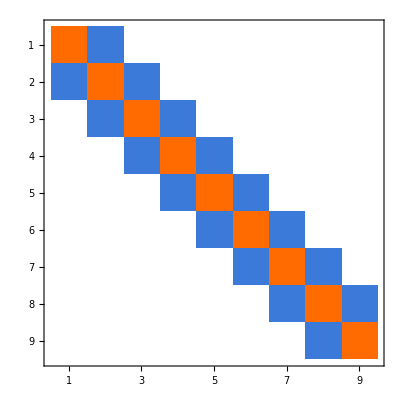

```mathematica
MatrixPlot@matrix@10
```

## «Кластеринг» собственных чисел матрицы

```mathematica
(*Λ[n_]:=Eigenvalues@A[n];*)
eigenValues[n_]:=Table[4n (Sin@((π k)/(2n)))^2,{k,n-1}] (* (3.35) *)
(*V[n_]:=Eigenvectors@A[n];*)
eigenVectors[n_]:=Table[Sin[i(π k)/n],{i,n-1},{k,n-1}] (* (3.35) *)
spectrumCond[n_]:=(Max@Map[Abs,eigenValues@n])/(Min@Map[Abs,eigenValues@n]) (* спектральная обусловленность матрицы *)
```

### Графики

```mathematica
n=91; (* максимальное число КЭ для визуализации *)
```

```mathematica
eigenPlots[n_]:=Table[
ListPlot[Map[({#,0})&,eigenValues@i],
PlotLabel->"n = "<>ToString@i,
Axes-> {True,False},
AxesLabel->{"λ"},
PlotRange->{{Min@eigenValues@n-5,Max@eigenValues@n+5},Automatic}, 
PlotStyle->PointSize[Medium],
ImageSize->800],
{i,2,n}]
ListAnimate@eigenPlots@n
```

```mathematica
spectrumCondPlot=DiscretePlot[spectrumCond@i,{i,2,n},AxesLabel->{"n","y"},PlotLegends->{"κ(A)"}];
```

```mathematica
spectrumCondFunc[y_]=FindFormula[Table[spectrumCond@i,{i,2,n}],y];
spectrumCondFunc@y
```

-0.251967+0.810179 y+0.405288 y^2

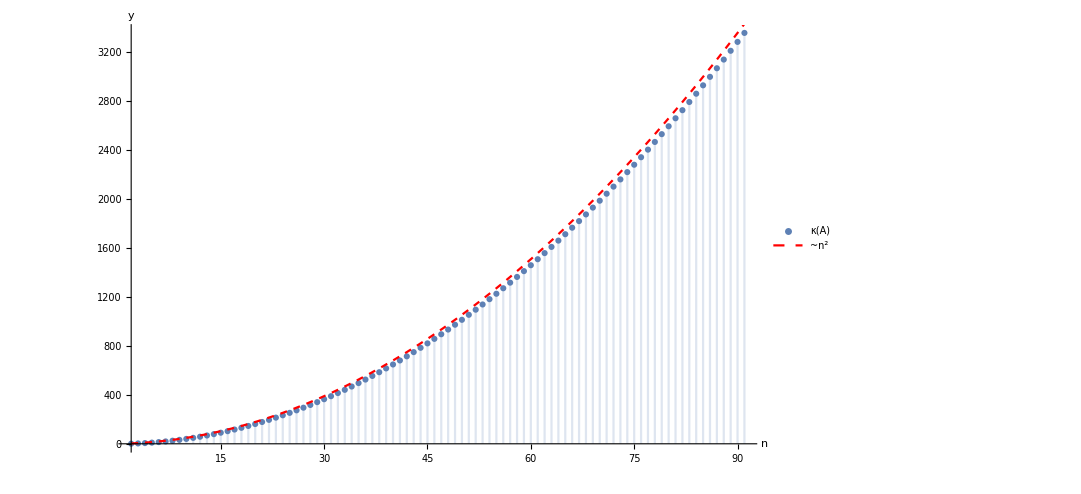

```mathematica
Show[spectrumCondPlot,Plot[spectrumCondFunc@x,{x,2,n},PlotStyle->{Red,Dashed},PlotLegends->{"~n^2"}],ImageSize->800]
```

## Сглаживание

```mathematica
A=N@matrix@n;
Λ=N@eigenValues@n;
V=N@Map[Normalize,eigenVectors@n];
```

```mathematica
x=Table[1.,{i,n-1}]; (* решение системы *)
b=A.x; (* правая часть *)
```

Подберём исходную невязку r_0 так, чтобы она имела одинаковые проекции на все собственные векторы матрицы A.

```mathematica
Subscript[ξ, 0]=50;
Subscript[r, 0]=Subscript[ξ, 0] Sum[V[[i]],{i,n-1}]; (* исходная невязка *)
Subscript[x, 0]=(* A^-1.(b - Subscript[r, 0]) = … = *)  Chop[Transpose@V.DiagonalMatrix@Map[1/#&,Λ].V].(b-Subscript[r, 0]);
```

```mathematica
ν=100; (* количество сглаживающих итераций *)
ω=1/(Max@Map[Abs,Λ]);
Do[
Subscript[x, i]=Subscript[x, i-1]+ ω Subscript[r, i-1];
Subscript[r, i]=b-A.Subscript[x, i]
,{i,ν}]
```

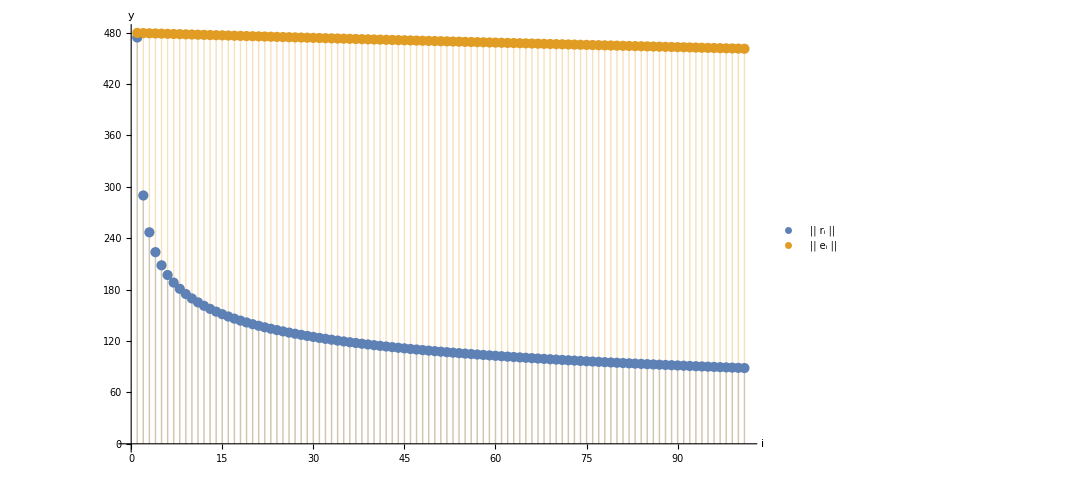

```mathematica
residuals=Table[Subscript[r, i],{i,0,ν}];
errors=Table[x-Subscript[x, i],{i,0,ν}];
ListPlot[{Map[Norm,residuals],Map[Norm,errors]},
PlotLegends->{"|| r_i ||","|| e_i ||"},
AxesLabel->{"i","y"},
Filling->Axis,
ImageSize->800]
```

```mathematica
Ξ=Table[Subscript[r, i-1].V[[j]],{i,ν+1},{j,n-1}];
residualComponents=Table[ListPlot[Ξ[[i]],
Filling->Axis,
PlotRange->{Automatic,{0,Subscript[ξ, 0]+1}},
PlotLabel->"ν = "<>ToString[i-1],
AxesLabel->{"i","(r_ν, v_i)"},
ImageSize->800
],{i,ν+1}];
```

```mathematica
ListAnimate@residualComponents
```

Компоненты невязки, соответствующие высокочастотным собственным векторам, падают (сглаживаются) очень быстро. Низкочастотные же компоненты оставляют нормы невязки большой.

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["residualComponentsJacobi.swf",residualComponents]*)
```

## Благоприятные (и не очень) спектральные характеристики матрицы для Крыловских решателей

```mathematica
n=501;
```

```mathematica
eigenValuesB1=N@eigenValues@n;
eigenValuesB2=Join[
{eigenValuesB1[[1]],eigenValuesB1[[-1]]},
Table[eigenValuesB1[[1]]+i(eigenValuesB1[[-1]]-eigenValuesB1[[1]])/(n-2),{i,n-3}]
];
eigenValuesB3=Join[
{eigenValuesB1[[1]]/10,10eigenValuesB1[[-1]]},
eigenValuesB2[[3;;]]
];
(*eigenValuesB3=Join[
{eigenValuesB1[[1]],eigenValuesB1[[-1]],eigenValuesB1[[-1]]/3,(2eigenValuesB1[[-1]])/3},
Table[eigenValuesB1[[-1]]/3+i(2eigenValuesB1[[-1]]-eigenValuesB1[[-1]])/(3(n-4)),{i,n-5}]
];*)
```

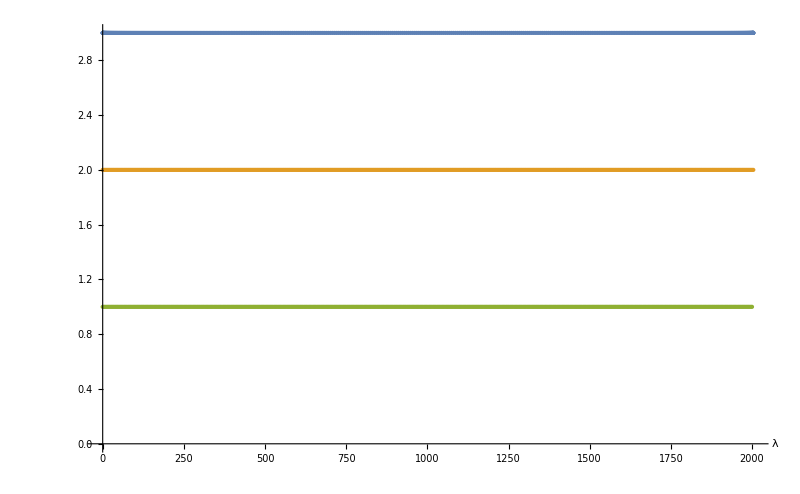

```mathematica
ListPlot[{
Map[({#,3})&,eigenValuesB1],
Map[({#,2})&,eigenValuesB2],
Map[({#,1})&,eigenValuesB3]
},
Axes-> {True,False},
AxesLabel->{"λ"},
PlotRange->{{eigenValuesB1[[1]]-5,eigenValuesB1[[-1]]+5},Automatic}, 
PlotStyle->PointSize[Small],
ImageSize->800]
```

### CG–метод

```mathematica
CG[A_,b_,x0_]:=Module[{errors,r,rxr,rxrNew,Axp,p,α,x},
x=x0;
r=b-A.x;
p=r;
rxr=r.r;
errors={};
Do[
If[Chop@rxr==0.,Break[]];
Axp=A.p;
α=rxr/(Axp.p);
x+=α p;
r-=α Axp;
rxrNew=r.r;
p=r+rxrNew/rxr p;
rxr=rxrNew;
AppendTo[errors,Table[1.,{j,n-1}]-x],{i,n-1}];
errors
]
```

```mathematica
B1=DiagonalMatrix@eigenValuesB1;
B2=DiagonalMatrix@eigenValuesB2;
B3=DiagonalMatrix@eigenValuesB3;
r0=Table[10,{i,n-1}];
```

```mathematica
errB1=CG[(* matrix *) B1,(* RHS *) eigenValuesB1,(* Subscript[x, 0], такой что каждая компонента Subscript[r, 0] в базисе собственных векторов = 50 *)DiagonalMatrix@Map[1/#&,eigenValuesB1].(eigenValuesB1-r0)];
errB2=CG[B2,eigenValuesB2,DiagonalMatrix@Map[1/#&,eigenValuesB2].(eigenValuesB2-r0)];
errB3=CG[B3,eigenValuesB3,DiagonalMatrix@Map[1/#&,eigenValuesB3].(eigenValuesB3-r0)];
```

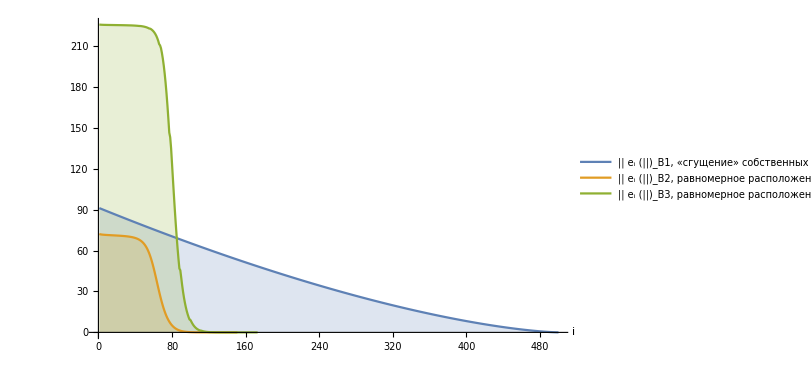

```mathematica
ListLinePlot[{
Map[Sqrt[#.B1.#]&,errB1],
Map[Sqrt[#.B2.#]&,errB2],
Map[Sqrt[#.B3.#]&,errB3]
},
PlotLegends->{
"|| e_i (||)_B1, «сгущение» собственных чисел",
"|| e_i (||)_B2, равномерное расположение собственных чисел, κ(B2) = κ(B1)",
"|| e_i (||)_B3, равномерное расположение собственных чисел, λ_1 « λ_2 и λ_(n - 2) « λ_(n - 1), κ(B3) = 100 κ(B1)"
},
AxesLabel->{"i",None},
Filling->Axis,
PlotRange->All,
ImageSize->600]
```

## Для презентации

```mathematica
n=60;
height=(Min@eigenValues@n+Max@eigenValues@n+10.)/10;
```

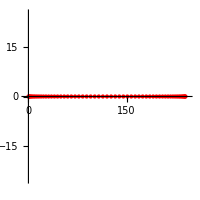

```mathematica
ListPlot[Map[({#,0})&,eigenValues@n],
Axes-> {True,False},
PlotRange->{{Min@eigenValues@n-5,Max@eigenValues@n+5},{-height,height}},
AspectRatio->Automatic, 
PlotStyle->{Red,PointSize[Medium]},
ImageSize->200]
```

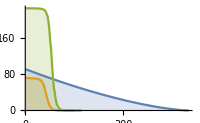

```mathematica
ListLinePlot[{
Map[Sqrt[#.B1.#]&,errB1],
Map[Sqrt[#.B2.#]&,errB2],
Map[Sqrt[#.B3.#]&,errB3]
},
Filling->Axis,
PlotRange->All,
ImageSize->200]
```